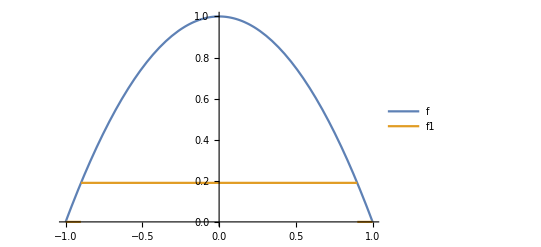

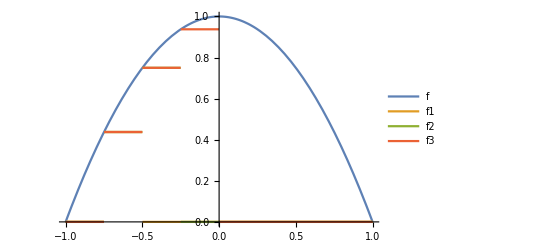

```mathematica
δ=9/10;
f0[x_]:=0;
f[x_]:=-x^2+1;
f1[x_]:=f0[x]+Piecewise[
{{f[δ],-δ≤x≤δ}},
0
];


Plot[{
Legended[f[x],"f"],
Legended[f1[x],"f1"]},
{x,-1,1}]


f1[x_]:=f0[x]+Piecewise[
{{f[-1+0.25],-1+0.25≤x≤-1+0.5}},
0
];
f2[x_]:=f1[x]+Piecewise[
{{f[-1+0.5],-1+0.5≤x≤-1+0.75}},
0
];
f3[x_]:=f2[x]+Piecewise[
{{f[-1+0.75],-1+0.75≤x≤-1+1}},
0
];
Plot[{
Legended[f[x],"f"],
Legended[f1[x],"f1"],
Legended[f2[x],"f2"],
Legended[f3[x],"f3"]},
{x,-1,1}]
```